```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/github_public_repos/d-Cubic/examples/test_deriv_x_1d

Grid

```mathematica
grid=Import["test_deriv_x_1d.txt","Table"];
```

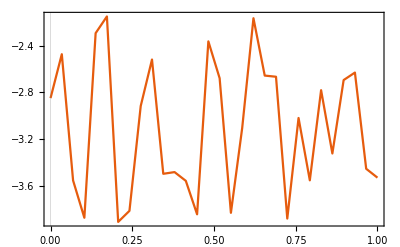

```mathematica
ListLinePlot[grid]
```

```mathematica
xSpacing=Abs[grid[[2,1]]-grid[[1,1]]]
```

0.0344828

Analytic formula

```mathematica
derivx=-0.5 p0+0.5 p2+2 (p0-2.5 p1+2. p2-0.5 p3) x+3 (-0.5 p0+1.5 p1-1.5 p2+0.5 p3) x^2
```

-0.5 p0+0.5 p2+2 (p0-2.5 p1+2. p2-0.5 p3) x+3 (-0.5 p0+1.5 p1-1.5 p2+0.5 p3) x^2

Test point

```mathematica
xTest=0.46;
```

Convert to fraction

```mathematica
pt1=Select[grid,#[[1]]>xTest-xSpacing&&#[[1]]<xTest&][[1]]
```

{0.448276,-3.8433}

```mathematica
xFrac=(xTest-pt1[[1]])/xSpacing
```

0.339996

Other pts

```mathematica
p=Association[];
Do[
p[i]=Select[grid,#[[1]]>xTest+(i-2)*xSpacing&&#[[1]]<xTest+(i-1)*xSpacing&][[1,2]];
,{i,0,3}];
```

Evaluate test

```mathematica
derivx/.{x->xFrac,p0->p[0],p1->p[1],p2->p[2],p3->p[3]}
```

1.79129